# Mushrooms — Edible or Poisonous?

### Training a neural network to predict if a mushroom is edible or poisonous

```mathematica
Hyperlink["http://archive.ics.uci.edu/ml/datasets/Mushroom"]
```

```mathematica
rawdata=Import["http://archive.ics.uci.edu/ml/machine-learning-databases/mushroom/agaricus-lepiota.data","CSV"];
```

```mathematica
RandomSample[rawdata,10]//Grid[#,Frame->All]&
```

e | x | f | g | t | n | f | c | b | u | t | b | s | s | w | g | p | w | o | p | n | v | d
p | f | s | w | t | p | f | c | n | w | e | e | s | s | w | w | p | w | o | p | n | v | g
p | f | y | c | f | m | f | c | b | y | e | c | k | y | c | c | p | w | n | n | w | c | d
e | f | y | n | t | n | f | c | b | w | t | b | s | s | g | p | p | w | o | p | n | v | d
p | k | y | e | f | y | f | c | n | b | t | ? | s | k | p | w | p | w | o | e | w | v | d
e | x | y | e | t | n | f | c | b | n | t | b | s | s | g | w | p | w | o | p | n | v | d
e | f | s | n | f | n | a | c | b | n | e | ? | s | s | o | o | p | n | o | p | o | c | l
e | f | y | g | t | n | f | c | b | n | t | b | s | s | w | w | p | w | o | p | n | v | d
p | f | y | g | f | f | f | c | b | p | e | b | k | k | n | p | p | w | o | l | h | v | d
p | f | s | e | f | y | f | c | n | b | t | ? | k | s | w | p | p | w | o | e | w | v | d

#### xx

```mathematica
labelEncoding=ImportString["1. cap-shape:                bell=b,conical=c,convex=x,flat=f,knobbed=k,sunken=s
     2. cap-surface:              fibrous=f,grooves=g,scaly=y,smooth=s
     3. cap-color:                brown=n,buff=b,cinnamon=c,gray=g,green=r,pink=p,purple=u,red=e,white=w,yellow=y
     4. bruises?:                 bruises=t,no=f
     5. odor:                     almond=a,anise=l,creosote=c,fishy=y,foul=f,musty=m,none=n,pungent=p,spicy=s
     6. gill-attachment:          attached=a,descending=d,free=f,notched=n
     7. gill-spacing:             close=c,crowded=w,distant=d
     8. gill-size:                broad=b,narrow=n
     9. gill-color:               black=k,brown=n,buff=b,chocolate=h,gray=g,green=r,orange=o,pink=p,purple=u,red=e,white=w,yellow=y
    10. stalk-shape:              enlarging=e,tapering=t
    11. stalk-root:               bulbous=b,club=c,cup=u,equal=e,rhizomorphs=z,rooted=r,missing=?
    12. stalk-surface-above-ring: fibrous=f,scaly=y,silky=k,smooth=s
    13. stalk-surface-below-ring: fibrous=f,scaly=y,silky=k,smooth=s
    14. stalk-color-above-ring:   brown=n,buff=b,cinnamon=c,gray=g,orange=o,pink=p,red=e,white=w,yellow=y
    15. stalk-color-below-ring:   brown=n,buff=b,cinnamon=c,gray=g,orange=o,pink=p,red=e,white=w,yellow=y
    16. veil-type:                partial=p,universal=u
    17. veil-color:               brown=n,orange=o,white=w,yellow=y
    18. ring-number:              none=n,one=o,two=t
    19. ring-type:                cobwebby=c,evanescent=e,flaring=f,large=l,none=n,pendant=p,sheathing=s,zone=z
    20. spore-print-color:        black=k,brown=n,buff=b,chocolate=h,green=r,orange=o,purple=u,white=w,yellow=y
    21. population:               abundant=a,clustered=c,numerous=n,scattered=s,several=v,solitary=y
    22. habitat:                  grasses=g,leaves=l,meadows=m,paths=p,urban=u,waste=w,woods=d",
"Lines"];
```

```mathematica
rules=Join[
{{"e"->"edible","p"->"poisonous"}},
Map[
StringCases[#,(a:LetterCharacter..)~~"="~~(b:LetterCharacter|"?"):>(b->a)]&,
labelEncoding]];
```

```mathematica
Length[rules]
```

23

#### xx

```mathematica
Length[rawdata]
```

8124

```mathematica
rawdataTransposed=Transpose[rawdata];
```

```mathematica
Length[rawdataTransposed]
```

23

```mathematica
rawdataProcessed=MapThread[#1/.#2&,{rawdataTransposed,rules}];
```

```mathematica
rawdataLabeled=Transpose[rawdataProcessed];
```

```mathematica
rawdata[[1]]
```

{p,x,s,n,t,p,f,c,n,k,e,e,s,s,w,w,p,w,o,p,k,s,u}

```mathematica
RandomSample[rawdataLabeled,5]
```

{{poisonous,flat,smooth,red,no,fishy,free,close,narrow,buff,tapering,missing,silky,silky,pink,pink,partial,white,one,evanescent,white,several,woods},{edible,convex,fibrous,white,no,none,free,crowded,broad,gray,enlarging,missing,silky,silky,white,white,partial,white,two,pendant,white,scattered,grasses},{edible,flat,scaly,gray,bruises,none,free,close,broad,pink,tapering,bulbous,smooth,smooth,white,gray,partial,white,one,pendant,brown,several,woods},{poisonous,flat,fibrous,yellow,no,foul,free,close,broad,pink,enlarging,bulbous,silky,silky,brown,brown,partial,white,one,large,chocolate,several,paths},{poisonous,convex,scaly,yellow,no,foul,free,close,broad,gray,enlarging,bulbous,silky,silky,brown,pink,partial,white,one,large,chocolate,solitary,grasses}}

```mathematica
Length[rawdataLabeled]
```

8124

```mathematica
Clear[rawdata2]
```

```mathematica
{rawdata1,rawdata2}=Partition[RandomSample[rawdataLabeled],5000,5000,1,{}];
Length/@{rawdata1,rawdata2}
```

{5000,3124}

```mathematica
rawdata1[[2]]
```

{edible,flat,fibrous,gray,bruises,none,free,close,broad,brown,tapering,bulbous,smooth,smooth,pink,gray,partial,white,one,pendant,black,solitary,woods}

```mathematica
keys={"result","cap-shape","cap-surface","cap-color","bruises","odor","gill-attachment","gill-spacing","gill-size","gill-color","stalk-shape","stalk-root","stalk-surface-above-ring","stalk-surface-below-ring","stalk-color-above-ring","stalk-color-below-ring","veil-type","veil-color","ring-number","ring-type","spore-print-color","population","habitat"};
```

```mathematica
Length[keys]
```

23

```mathematica
training=Dataset[
Map[
AssociationThread[keys->#]&,rawdata1]
]
```

Dataset[<>]

```mathematica
allLabels=Union/@Transpose[rawdataLabeled][[2;;-1]]
```

{{bell,conical,convex,flat,knobbed,sunken},{fibrous,grooves,scaly,smooth},{brown,buff,cinnamon,gray,green,pink,purple,red,white,yellow},{bruises,no},{almond,anise,creosote,fishy,foul,musty,none,pungent,spicy},{attached,free},{close,crowded},{broad,narrow},{black,brown,buff,chocolate,gray,green,orange,pink,purple,red,white,yellow},{enlarging,tapering},{bulbous,club,equal,missing,rooted},{fibrous,scaly,silky,smooth},{fibrous,scaly,silky,smooth},{brown,buff,cinnamon,gray,orange,pink,red,white,yellow},{brown,buff,cinnamon,gray,orange,pink,red,white,yellow},{partial},{brown,orange,white,yellow},{none,one,two},{evanescent,flaring,large,none,pendant},{black,brown,buff,chocolate,green,orange,purple,white,yellow},{abundant,clustered,numerous,scattered,several,solitary},{grasses,leaves,meadows,paths,urban,waste,woods}}

```mathematica
encoders=
Table[
NetEncoder[{"Class",label,"UnitVector"}],
{label,allLabels}];
```

```mathematica
Manipulate[
Grid[Map[{#,encoders[[a]][#]}&,allLabels[[a]]],Frame->All],
{a,1,22,1}]
```

Part::partd: Part specification allLabels⟦5⟧ is longer than depth of object.

Part::partd: Part specification encoders⟦5⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::pkspec1: The expression {5,encoders⟦5⟧[5]} cannot be used as a part specification.

Part::partd: Part specification encoders⟦5⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

```mathematica
netports=Rest[NetPort/@keys]
```

{NetPort[cap-shape],NetPort[cap-surface],NetPort[cap-color],NetPort[bruises],NetPort[odor],NetPort[gill-attachment],NetPort[gill-spacing],NetPort[gill-size],NetPort[gill-color],NetPort[stalk-shape],NetPort[stalk-root],NetPort[stalk-surface-above-ring],NetPort[stalk-surface-below-ring],NetPort[stalk-color-above-ring],NetPort[stalk-color-below-ring],NetPort[veil-type],NetPort[veil-color],NetPort[ring-number],NetPort[ring-type],NetPort[spore-print-color],NetPort[population],NetPort[habitat]}

```mathematica
port2encoders=MapThread[Rule,{Rest[keys],encoders}];
```

```mathematica
net=NetGraph[{
CatenateLayer[],
DotPlusLayer[80],
ElementwiseLayer[Tanh],
DotPlusLayer[2],
SoftmaxLayer[]
},{
netports->1,
1->2,2->3,3->4,4->5,5->NetPort["result"]
},
Sequence@@port2encoders,
"result"->NetDecoder[{"Class",{"edible","poisonous"}}]
]
```

NetGraph[]

```mathematica
result=NetTrain[net,training];
```

```mathematica
validation=Table[r[[2;;-1]]->r[[1]],{r,rawdata2}];
```

```mathematica
validation[[10]]
```

{convex,scaly,red,bruises,none,free,close,broad,purple,tapering,bulbous,smooth,smooth,gray,white,partial,white,one,pendant,black,solitary,woods}→edible

```mathematica
Length[validation]
```

2124

```mathematica
cm=ClassifierMeasurements[result,validation];
```

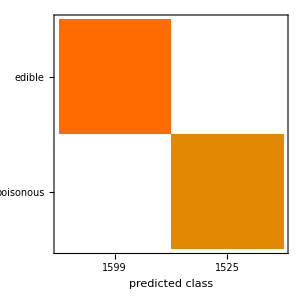

```mathematica
cm["ConfusionMatrixPlot"]
```